# Corner Flow general solution

```mathematica
vx = -B-D*ArcTan[x,z] + (C*x + D*z)(-x/(x^2+z^2))
vz = A+C*ArcTan[x,z] + (C*x + D*z)(-z/(x^2+z^2))
```

-B-(x (C x+D z))/(x^2+z^2)-D ArcTan[x,z]

A-(z (C x+D z))/(x^2+z^2)+C ArcTan[x,z]

## Specify dip angle of subduction zone

```mathematica
δval = 45*Pi/180;
```

## Apply boundary conditions for continental arc corner flow

```mathematica
eq1 = ReplaceAll[vx,{ArcTan[x,z]->0,z->0}]
eq2 = ReplaceAll[vz,{ArcTan[x,z]->0,z->0}]
eq3=ReplaceAll[vx,{ArcTan[x,z]->-δ,z->-x*Tan[δ]}]
eq4=ReplaceAll[vz,{ArcTan[x,z]->-δ,z->-x*Tan[δ]}]
solarc =Solve[eq1==0&&eq2==0&&eq3==Cos[δ]&&eq4==-Sin[δ],{A,B,C,D},Reals,Assumptions->{δ>0,δ<Pi/2}]
```

-B-C

A

-B+D δ-(x (C x-D x Tan[δ]))/(x^2+x^2 Tan[δ]^2)

A-C δ+(x Tan[δ] (C x-D x Tan[δ]))/(x^2+x^2 Tan[δ]^2)

{{A→0,B→-(2 Cos[δ]-2 Cos[δ] Cos[2 δ]-4 δ Sin[δ]-2 Sin[δ] Sin[2 δ])/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2),C→(2 Cos[δ]-2 Cos[δ] Cos[2 δ]-4 δ Sin[δ]-2 Sin[δ] Sin[2 δ])/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2),D→(2 Cos[δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-(Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2 Cos[δ]-2 Cos[δ] Cos[2 δ]-4 δ Sin[δ]-2 Sin[δ] Sin[2 δ]))/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2)+(Cos[2 δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2 Cos[δ]-2 Cos[δ] Cos[2 δ]-4 δ Sin[δ]-2 Sin[δ] Sin[2 δ]))/(1-4 δ^2-2 Cos[2 δ]+Cos[2 δ]^2+Sin[2 δ]^2))/(2 δ Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2+Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 Sin[2 δ])}}

```mathematica
solplot=ReplaceAll[solarc,{δ->δval}];
Aval=A/.solplot[[1]]
Bval=B/.solplot[[1]]//FullSimplify
Cval=C/.solplot[[1]]//FullSimplify
Dval=D/.solplot[[1]]//FullSimplify
```

0

-(2 √2 π)/(-8+π^2)

(2 √2 π)/(-8+π^2)

(2 √2 (-4+π))/(-8+π^2)

# Plot velocity field

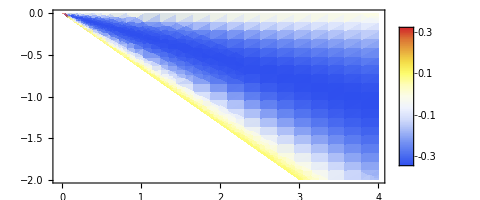

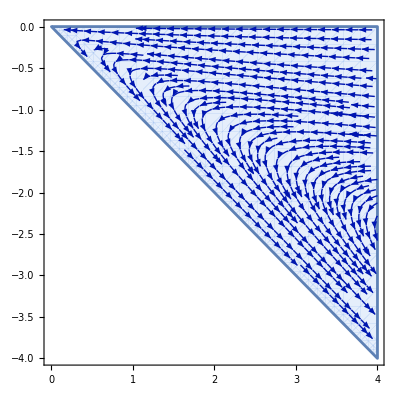

```mathematica
toplotxc=ReplaceAll[vx,{A->Aval,B->Bval,C->Cval,D->Dval}];
toplotzc=ReplaceAll[vz,{A->Aval,B->Bval,C->Cval,D->Dval}];
(*D[toplotx,z]+D[toplotz,x]//FullSimplify*)
DensityPlot[toplotxc,{x,-0.04,4},{z,-2,0},PlotLegends->Automatic,PlotPoints->20,ColorFunction->"TemperatureMap",RegionFunction->Function[{x,z},0>=Tan[z/x]>=-δval],AspectRatio->Automatic]
(*RegionFunction->Function[{x,z},0>=Tan[z/x]>=-δval]*)
p1=StreamPlot[{toplotxc,toplotzc},{x,-0.01,4},{z,-4*Tan[δval],0},RegionFunction->Function[{x,z},z+Tan[δval]*x>=0 && x>=0.0],StreamPoints->Fine,StreamScale->Tiny,AspectRatio->Automatic]
```

## Insert boundary conditions for oceanic mantle

```mathematica
eq1 = ReplaceAll[vx,{ArcTan[x,z]->-π,z->0}]
eq2 = ReplaceAll[vz,{ArcTan[x,z]->-π,z->0}]
eq3=ReplaceAll[vx,{ArcTan[x,z]->-δ,z->-x*Tan[δ]}]
eq4=ReplaceAll[vz,{ArcTan[x,z]->-δ,z->-x*Tan[δ]}]
solocean =Solve[eq1==1&&eq2==0&&eq3==Cos[δ]&&eq4==-Sin[δ],{A,B,C,D},Reals,Assumptions->{δ>0,δ<Pi/2}]
```

-B-C+D π

A-C π

-B+D δ-(x (C x-D x Tan[δ]))/(x^2+x^2 Tan[δ]^2)

A-C δ+(x Tan[δ] (C x-D x Tan[δ]))/(x^2+x^2 Tan[δ]^2)

{{A→(π (2-2 Cos[δ]-2 Cos[2 δ]+2 Cos[δ] Cos[2 δ]-4 π Sin[δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ]))/(-1+4 π^2-8 π δ+4 δ^2+2 Cos[2 δ]-Cos[2 δ]^2-Sin[2 δ]^2),B→-1-(2-2 Cos[δ]-2 Cos[2 δ]+2 Cos[δ] Cos[2 δ]-4 π Sin[δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ])/(-1+4 π^2-8 π δ+4 δ^2+2 Cos[2 δ]-Cos[2 δ]^2-Sin[2 δ]^2)+(π (2 Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-2 Cos[δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2+(Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2-2 Cos[δ]-2 Cos[2 δ]+2 Cos[δ] Cos[2 δ]-4 π Sin[δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ]))/(-1+4 π^2-8 π δ+4 δ^2+2 Cos[2 δ]-Cos[2 δ]^2-Sin[2 δ]^2)-(Cos[2 δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2-2 Cos[δ]-2 Cos[2 δ]+2 Cos[δ] Cos[2 δ]-4 π Sin[δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ]))/(-1+4 π^2-8 π δ+4 δ^2+2 Cos[2 δ]-Cos[2 δ]^2-Sin[2 δ]^2)))/(2 π Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-2 δ Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 Sin[2 δ]),C→(2-2 Cos[δ]-2 Cos[2 δ]+2 Cos[δ] Cos[2 δ]-4 π Sin[δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ])/(-1+4 π^2-8 π δ+4 δ^2+2 Cos[2 δ]-Cos[2 δ]^2-Sin[2 δ]^2),D→(2 Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-2 Cos[δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2+(Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2-2 Cos[δ]-2 Cos[2 δ]+2 Cos[δ] Cos[2 δ]-4 π Sin[δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ]))/(-1+4 π^2-8 π δ+4 δ^2+2 Cos[2 δ]-Cos[2 δ]^2-Sin[2 δ]^2)-(Cos[2 δ] Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 (2-2 Cos[δ]-2 Cos[2 δ]+2 Cos[δ] Cos[2 δ]-4 π Sin[δ]+4 δ Sin[δ]+2 Sin[δ] Sin[2 δ]))/(-1+4 π^2-8 π δ+4 δ^2+2 Cos[2 δ]-Cos[2 δ]^2-Sin[2 δ]^2))/(2 π Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-2 δ Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2-Csc[π/4-δ/2]^2 Csc[π/4+δ/2]^2 Sin[2 δ])}}

```mathematica
solplot=ReplaceAll[solocean,{δ->δval}];
Aval=A/.solplot[[1]]
Bval=B/.solplot[[1]]//FullSimplify
Cval=C/.solplot[[1]]//FullSimplify
Dval=D/.solplot[[1]]//FullSimplify
```

(π (2+π/(√2)-2 √2 π))/(-2+(9 π^2)/4)

(π (8-2 √2+(3-6 √2) π))/(-8+9 π^2)

(8-6 √2 π)/(-8+9 π^2)

(8-8 √2-6 (-2+√2) π)/(-8+9 π^2)

# Plot velocity field

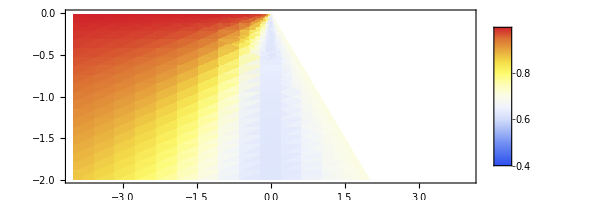

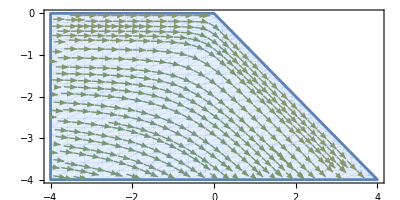

```mathematica
toplotxo=ReplaceAll[vx,{A->Aval,B->Bval,C->Cval,D->Dval}];
toplotzo=ReplaceAll[vz,{A->Aval,B->Bval,C->Cval,D->Dval}];
DensityPlot[toplotxo,{x,-4,4},{z,-2,0},PlotLegends->Automatic,PlotPoints->20,ColorFunction->"TemperatureMap",RegionFunction->Function[{x,z},z+Tan[δval]*x<=0],AspectRatio->Automatic]
p2=StreamPlot[{toplotxo,toplotzo},{x,-4,4},{z,-4*Tan[δval],0},StreamPoints->Fine,StreamScale->Tiny,AspectRatio->Automatic,RegionFunction->Function[{x,z},z+Tan[δval]*x<=0 ],StreamColorFunction->"ArmyColors"]
```

# Show oceanic and continental corner flow

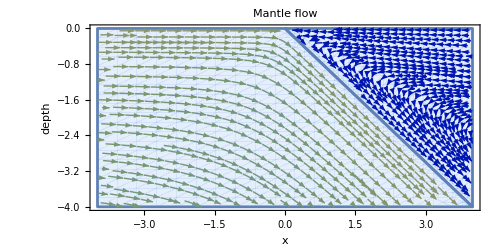

```mathematica
Show[p1,p2,PlotRange->All,AspectRatio->Automatic,ImageSize->500,PlotLabel->"Mantle flow",FrameLabel->{"x","depth"},BaseStyle->{FontSize->16}]
```